```mathematica
a=0.7;
b=0.8;
c=3;
R=1;
τinv=0.08 ;
Iext=0.5;

vp[v_,w_]:=v-v^3-w+R*Iext;
wp[v_,w_]:=(τinv)*(v+a-b*w)
```

Lets try a stream plot to see what the phase looks like???

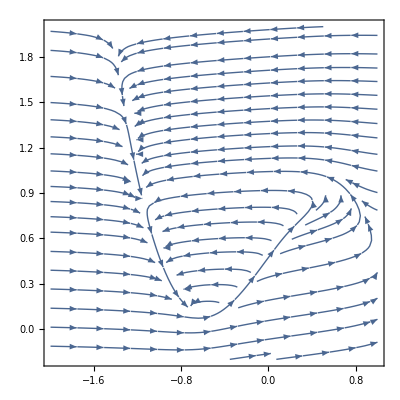

```mathematica
StreamPlot[{vp[v,w],wp[v,w]},{v,-2,1},{w,-0.2,2}]
```